# 2-loop electron self-enegery with IREG

## Electron Bubble Diagram

## FeynCalc with FeynArts and TARCER

```mathematica
(*Load FeynCalc with FeynArts and the package TARCER*)
```

```mathematica
description="Electron self-energy at 2-loop with IREG-Electron Bubble";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"TARCER","FeynArts"};
Get["FeynCalc`"]
$FAVerbose=0;
FCCheckVersion[9,3,0];
$Comment=True;
Off[General::"spell"];
Off[General::"spell1"];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

TARCER 2.0, for more information see the accompanying publication. If you use TARCER in your research, please cite

• R. Mertig and R. Scharf, Comput. Phys. Commun., 111, 265-273, 1998, arXiv:hep-ph/9801383

FeynArts 3.11 (3 Aug 2020) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

## Fermion to Fermion process defined

```mathematica
ClearProcess[];
Processee={F[2,{1}]}->{F[2,{1}]};
SetOptions[InsertFields,InsertionLevel->{Particles},Model->FileNameJoin[{"QED","QED"}],GenericModel->FileNameJoin[{"QED","QED"}],ExcludeParticles->{F[2,{2|3}]}];
```

## Topology Generation with FeynArts

```mathematica
(*Topology creation with FeynArts function CreateTopologies[]. 1PI 2-loop topology for a 1->1 fermion (F[2,{1}]) process is generated. Default options for FeynArts function InsertFields[] are set*)
```

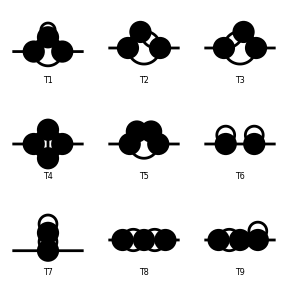

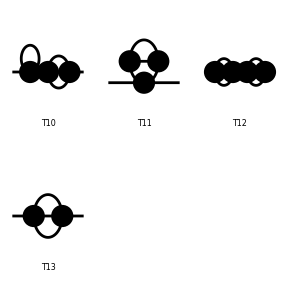

```mathematica
Topologiesfermions=CreateTopologies[2,1->1,ExcludeTopologies->{Tadpoles}];
Paint[Topologiesfermions];
```

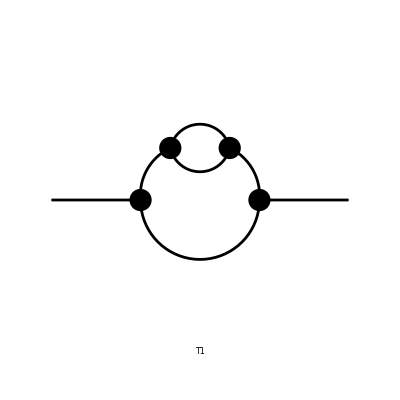

FeynArtsGraphics(1→1)(([T1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
bubbletopologies=Take[Topologiesfermions,{5}];
Paint[bubbletopologies]
```

## Diagram generation with fields

```mathematica
(*We substitute the propagators and external fields from QED in previous selected topology*)
```

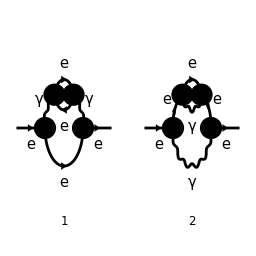

```mathematica
bubbleWITHfields=InsertFields[bubbletopologies,Processee,ExcludeParticles->{S[_],V[2|3],(S|U)[_],F[3|4],F[2,{2|3}]}];
Paint[bubbleWITHfields,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

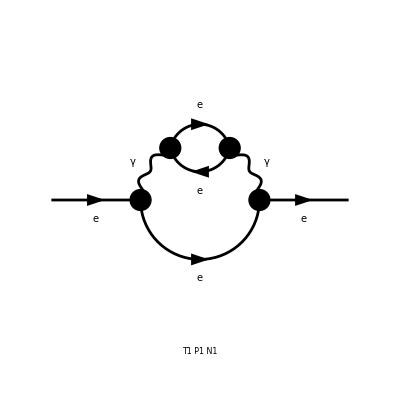

FeynArtsGraphics({e}→{e})(([T1 P1 N1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
theelectronBubble=DiagramExtract[bubbleWITHfields,1];
Paint[theelectronBubble]
```

## Amplitude (no regularized)

```mathematica
(*Amplitude is generated in FeynArts with function CreateFeynAmp[]. This expression is later conver to FeynCalc using FCFAConvert[]. Feynman gauge Subscript[ξ, g]=1 is chose later*)
```

```mathematica
FAamplElectronB=CreateFeynAmp[theelectronBubble,Truncated->True,GaugeRules->{},PreFactor->1];
```

### In 4-dim (for IREG integrals)

```mathematica
(*Notice that we set in FCFAConvert options that ChangeDimensions->4*)
```

```mathematica
convertamplElectronB2=FCFAConvert[FAamplElectronB,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{l,k},LorentzIndexNames->{μ,ν,α,β},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,DropSumOver->True,Contract->True];
```

```mathematica
(*We work now in Feynman gauge*)
```

```mathematica
FeynmangaugeamplElectronB2=convertamplElectronB2/. GaugeXi[V[1]] -> 1
```

(ⅈ e^2 (γ̄)^β.(γ̄·l̄+m_e).(γ̄)^ν tr(e^2 (-(m_e-γ̄·k̄).(γ̄)^ν.(γ̄·(-k̄+l̄-p̄)+m_e).(γ̄)^β)))/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((-k̄+l̄-p̄)^2-m_e^2))

```mathematica
AlgebraDiracElectronB2A=DiracSimplify[FeynmangaugeamplElectronB2]
```

-(4 ⅈ (γ̄)^ν.(γ̄)^ν e^4 m_e^3)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((k̄-l̄+p̄)^2-m_e^2))-(4 ⅈ (γ̄)^ν.(γ̄·l̄).(γ̄)^ν e^4 m_e^2)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((k̄-l̄+p̄)^2-m_e^2))-(8 ⅈ (γ̄·k̄).(γ̄·l̄).(γ̄·k̄) e^4)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((k̄-l̄+p̄)^2-m_e^2))+(4 ⅈ (γ̄·k̄).(γ̄·l̄).(γ̄·l̄) e^4)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((k̄-l̄+p̄)^2-m_e^2))-(4 ⅈ (γ̄·k̄).(γ̄·l̄).(γ̄·p̄) e^4)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((k̄-l̄+p̄)^2-m_e^2))+(4 ⅈ (γ̄·l̄).(γ̄·l̄).(γ̄·k̄) e^4)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((k̄-l̄+p̄)^2-m_e^2))-(4 ⅈ (γ̄·p̄).(γ̄·l̄).(γ̄·k̄) e^4)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((k̄-l̄+p̄)^2-m_e^2))+(4 ⅈ (γ̄)^ν.(γ̄·l̄).(γ̄)^ν (k̄)^2 e^4)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((k̄-l̄+p̄)^2-m_e^2))-(4 ⅈ (γ̄)^ν.(γ̄·l̄).(γ̄)^ν (k̄·l̄) e^4)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((k̄-l̄+p̄)^2-m_e^2))+(4 ⅈ (γ̄)^ν.(γ̄·l̄).(γ̄)^ν (k̄·p̄) e^4)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((k̄-l̄+p̄)^2-m_e^2))-(8 ⅈ (γ̄·k̄).(γ̄·k̄) e^4 m_e)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((k̄-l̄+p̄)^2-m_e^2))+(4 ⅈ (γ̄·k̄).(γ̄·l̄) e^4 m_e)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((k̄-l̄+p̄)^2-m_e^2))-(4 ⅈ (γ̄·k̄).(γ̄·p̄) e^4 m_e)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((k̄-l̄+p̄)^2-m_e^2))+(4 ⅈ (γ̄·l̄).(γ̄·k̄) e^4 m_e)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((k̄-l̄+p̄)^2-m_e^2))-(4 ⅈ (γ̄·p̄).(γ̄·k̄) e^4 m_e)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((k̄-l̄+p̄)^2-m_e^2))+(4 ⅈ (γ̄)^ν.(γ̄)^ν (k̄)^2 e^4 m_e)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((k̄-l̄+p̄)^2-m_e^2))-(4 ⅈ (γ̄)^ν.(γ̄)^ν (k̄·l̄) e^4 m_e)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((k̄-l̄+p̄)^2-m_e^2))+(4 ⅈ (γ̄)^ν.(γ̄)^ν (k̄·p̄) e^4 m_e)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((k̄-l̄+p̄)^2-m_e^2))

```mathematica
(*It is hard to notice at first sight, but even using DiracSimplify, still there are some simplification we can still do with the matrices. So using DiracSimplify again will be necessary*)
```

```mathematica
(*Somo comments related ksquared terms will be done in a few lines*)
```

```mathematica
AlgebraDiracElectronC2A=DiracSimplify[AlgebraDiracElectronB2A];
```

```mathematica
FinalElectronBAmpforIREG=Simplify[AlgebraDiracElectronC2A]
```

-((4 ⅈ e^4 (-m_e (γ̄·k̄).(γ̄·l̄)-m_e (γ̄·l̄).(γ̄·k̄)+4 m_e (k̄·l̄)+m_e (γ̄·k̄).(γ̄·p̄)+m_e (γ̄·p̄).(γ̄·k̄)-4 m_e (k̄·p̄)-2 (k̄)^2 m_e-2 m_e^2 γ̄·l̄+4 γ̄·k̄ (k̄·l̄)-2 (k̄·l̄) γ̄·l̄-2 (l̄)^2 γ̄·k̄+2 (k̄·p̄) γ̄·l̄+(γ̄·k̄).(γ̄·l̄).(γ̄·p̄)+(γ̄·p̄).(γ̄·l̄).(γ̄·k̄)+4 m_e^3))/((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((k̄-l̄+p̄)^2-m_e^2))

## Integrals (mass case)

### Integrals-IREG

```mathematica
{irrelevantIREG,loops,THEUNIQUEIREGINTEGRALS}=FCLoopExtract[FinalElectronBAmpforIREG,{l,k},loopHeadIREG];
IREGINTEGRALSQB=THEUNIQUEIREGINTEGRALS/.loopHeadIREG->Identity
```

{1/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((-k̄+l̄-p̄)^2-m_e^2)),(γ̄·l̄)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((-k̄+l̄-p̄)^2-m_e^2)),((γ̄·k̄).(γ̄·l̄))/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((-k̄+l̄-p̄)^2-m_e^2)),((γ̄·k̄).(γ̄·p̄))/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((-k̄+l̄-p̄)^2-m_e^2)),((γ̄·l̄).(γ̄·k̄))/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((-k̄+l̄-p̄)^2-m_e^2)),((γ̄·p̄).(γ̄·k̄))/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((-k̄+l̄-p̄)^2-m_e^2)),((γ̄·k̄).(γ̄·l̄).(γ̄·p̄))/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((-k̄+l̄-p̄)^2-m_e^2)),((γ̄·p̄).(γ̄·l̄).(γ̄·k̄))/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((-k̄+l̄-p̄)^2-m_e^2)),(k̄)^2/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((-k̄+l̄-p̄)^2-m_e^2)),(k̄·l̄)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((-k̄+l̄-p̄)^2-m_e^2)),(γ̄·k̄ (k̄·l̄))/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((-k̄+l̄-p̄)^2-m_e^2)),((k̄·l̄) γ̄·l̄)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((-k̄+l̄-p̄)^2-m_e^2)),(k̄·p̄)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((-k̄+l̄-p̄)^2-m_e^2)),((k̄·p̄) γ̄·l̄)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((-k̄+l̄-p̄)^2-m_e^2)),((l̄)^2 γ̄·k̄)/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((-k̄+l̄-p̄)^2-m_e^2))}

## Working in the massless regime

```mathematica
(*To compute the counterterm of the electron field, we set the mass zero in the amplitude before doing the simplification of Dirac matrices*)
```

```mathematica
Print[FeynmangaugeamplElectronB2]
```

(ⅈ e^2 (γ̄)^β.(γ̄·l̄+m_e).(γ̄)^ν tr(e^2 (-(m_e-γ̄·k̄).(γ̄)^ν.(γ̄·(-k̄+l̄-p̄)+m_e).(γ̄)^β)))/(((l̄)^2-m_e^2).((k̄)^2-m_e^2).((l̄-p̄)^2)^2.((-k̄+l̄-p̄)^2-m_e^2))

```mathematica
(*We put the mass of the fermion zero to work in the massless regime*)
```

```mathematica
ElectronB2massless=FeynmangaugeamplElectronB2//.SMP["m_e"]->0
```

(ⅈ e^2 (γ̄)^β.(γ̄·l̄).(γ̄)^ν tr(e^2 (-(-(γ̄·k̄)).(γ̄)^ν.(γ̄·(-k̄+l̄-p̄)).(γ̄)^β)))/((l̄)^2.(k̄)^2.((l̄-p̄)^2)^2.(-k̄+l̄-p̄)^2)

```mathematica
(*Let's define then the general shift l->l+p for each part*)
```

```mathematica
ShiftA={Momentum[l]->Momentum[l+p]};
ShiftB={DiracGamma[Momentum[-k+l-p]]->(DiracGamma[Momentum[-k+l]])};
ShiftC={Momentum[l-p]->Momentum[l]};
ShiftD={Momentum[-k+l-p]->Momentum[-k+l]};
```

```mathematica
(*Sadly, in a define the general shift l->l+p in separated parts because if not I have conflicts with the substitution after*)
```

```mathematica
ElectronB2masslessSHIFA=ElectronB2massless//.ShiftA;
ElectronB2masslessSHIFB=ElectronB2masslessSHIFA//.ShiftB;
ElectronB2masslessSHIFC=ElectronB2masslessSHIFB//.ShiftC;
ElectronB2masslessSHIFD=ElectronB2masslessSHIFC//.ShiftD
```

(ⅈ e^2 (γ̄)^β.(γ̄·(l̄+p̄)).(γ̄)^ν tr(e^2 (-(-(γ̄·k̄)).(γ̄)^ν.(γ̄·(l̄-k̄)).(γ̄)^β)))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(l̄-k̄)^2)

```mathematica
AlgebraDiracElectronB2Amassless=DiracSimplify[ElectronB2masslessSHIFD]
```

-(4 ⅈ e^4 (k̄·l̄) (γ̄)^ν.(γ̄·l̄).(γ̄)^ν)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-(4 ⅈ e^4 (k̄·l̄) (γ̄)^ν.(γ̄·p̄).(γ̄)^ν)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (k̄)^2 (γ̄)^ν.(γ̄·l̄).(γ̄)^ν)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (k̄)^2 (γ̄)^ν.(γ̄·p̄).(γ̄)^ν)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+-(8 ⅈ e^4 (γ̄·k̄).(γ̄·l̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·k̄).(γ̄·l̄).(γ̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-(8 ⅈ e^4 (γ̄·k̄).(γ̄·p̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·k̄).(γ̄·p̄).(γ̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·l̄).(γ̄·l̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·l̄).(γ̄·p̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

```mathematica
(*When we do DiracSimplify after the shift, FeynCalc resolves the trace and do after the products with the part outside the trace. That process give us 10 different terms. From those 10 terms, we need to be careful with the ones that have (or give) k^2 terms. In IREG, symmetric integration is not allowed in divergent integrals so the integral with (ḡ)^αβ (k̄)^α (k̄)^β is not the same as the integral with (k̄)^2*)
```

```mathematica
-(4 ⅈ ("e")^4 (k̄"·"l̄) ((γ̄)^ν).(γ̄·l̄).(γ̄)^ν)/(("("l̄+p̄")")^2 .(k̄)^2 .(((l̄)^2)^2).("("k̄-l̄")")^2)-(4 ⅈ ("e")^4 (k̄"·"l̄) ((γ̄)^ν).(γ̄·p̄).(γ̄)^ν)/(("("l̄+p̄")")^2 .(k̄)^2 .(((l̄)^2)^2).("("k̄-l̄")")^2)+(4 ⅈ ("e")^4 (k̄)^2 ((γ̄)^ν).(γ̄·l̄).(γ̄)^ν)/(("("l̄+p̄")")^2 .(k̄)^2 .(((l̄)^2)^2).("("k̄-l̄")")^2)+(4 ⅈ ("e")^4 (k̄)^2 ((γ̄)^ν).(γ̄·p̄).(γ̄)^ν)/(("("l̄+p̄")")^2 .(k̄)^2 .(((l̄)^2)^2).("("k̄-l̄")")^2)+-(8 ⅈ ("e")^4 (γ̄·k̄).(γ̄·l̄).(γ̄·k̄))/(("("l̄+p̄")")^2 .(k̄)^2 .(((l̄)^2)^2).("("k̄-l̄")")^2)+(4 ⅈ ("e")^4 (γ̄·k̄).(γ̄·l̄).(γ̄·l̄))/(("("l̄+p̄")")^2 .(k̄)^2 .(((l̄)^2)^2).("("k̄-l̄")")^2)-(8 ⅈ ("e")^4 (γ̄·k̄).(γ̄·p̄).(γ̄·k̄))/(("("l̄+p̄")")^2 .(k̄)^2 .(((l̄)^2)^2).("("k̄-l̄")")^2)+(4 ⅈ ("e")^4 (γ̄·k̄).(γ̄·p̄).(γ̄·l̄))/(("("l̄+p̄")")^2 .(k̄)^2 .(((l̄)^2)^2).("("k̄-l̄")")^2)+(4 ⅈ ("e")^4 (γ̄·l̄).(γ̄·l̄).(γ̄·k̄))/(("("l̄+p̄")")^2 .(k̄)^2 .(((l̄)^2)^2).("("k̄-l̄")")^2)+(4 ⅈ ("e")^4 (γ̄·l̄).(γ̄·p̄).(γ̄·k̄))/(("("l̄+p̄")")^2 .(k̄)^2 .(((l̄)^2)^2).("("k̄-l̄")")^2)
```

-(4 ⅈ e^4 · k̄ l̄ (γ̄)^ν.(γ̄·l̄).(γ̄)^ν)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-(4 ⅈ e^4 · k̄ l̄ (γ̄)^ν.(γ̄·p̄).(γ̄)^ν)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (k̄)^2 (γ̄)^ν.(γ̄·l̄).(γ̄)^ν)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (k̄)^2 (γ̄)^ν.(γ̄·p̄).(γ̄)^ν)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-(8 ⅈ e^4 (γ̄·k̄).(γ̄·l̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·k̄).(γ̄·l̄).(γ̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-(8 ⅈ e^4 (γ̄·k̄).(γ̄·p̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·k̄).(γ̄·p̄).(γ̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·l̄).(γ̄·l̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·l̄).(γ̄·p̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

```mathematica
(*Notice this... the (k̄)^β (k̄)^ν (γ̄)^β.(γ̄·l̄).(γ̄)^ν and (k̄)^β (k̄)^ν (γ̄)^β.(γ̄·p̄).(γ̄)^ν in fact they will generate  (ḡ)^αβ (k̄)^α (k̄)^β. Again, in IREG  (ḡ)^αβ (k̄)^α (k̄)^β =/= (k̄)^2. The first is a finite term while the other generates an Iquad term that is null. At this point, it'll be interesting to create a little function that takes the previous expression and separates this terms... but here we will do it step by step*)
```

```mathematica
(*The integrals with the ksquared terms*)
```

```mathematica
IquadWithL=DiracGamma[LorentzIndex[ν]].DiracGamma[Momentum[l]].DiracGamma[LorentzIndex[ν]]Pair[Momentum[k],Momentum[k]]FeynAmpDenominator[PropagatorDenominator[Momentum[l+p],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[-Momentum[k-l],0]]
```

((k̄)^2 (γ̄)^ν.(γ̄·l̄).(γ̄)^ν)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

```mathematica
IquadWithP=DiracGamma[LorentzIndex[ν]].DiracGamma[Momentum[p]].DiracGamma[LorentzIndex[ν]]Pair[Momentum[k],Momentum[k]]FeynAmpDenominator[PropagatorDenominator[Momentum[l+p],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[-Momentum[k-l],0]]
```

((k̄)^2 (γ̄)^ν.(γ̄·p̄).(γ̄)^ν)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

```mathematica
FiniteWithL=DiracGamma[Momentum[k]].DiracGamma[Momentum[l]].DiracGamma[Momentum[k]]FeynAmpDenominator[PropagatorDenominator[Momentum[l+p],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[-Momentum[k-l],0]]
```

((γ̄·k̄).(γ̄·l̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

```mathematica
FiniteWithP=DiracGamma[Momentum[k]].DiracGamma[Momentum[p]].DiracGamma[Momentum[k]]FeynAmpDenominator[PropagatorDenominator[Momentum[l+p],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[-Momentum[k-l],0]]
```

((γ̄·k̄).(γ̄·p̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

```mathematica
(*The remplacements*)
```

```mathematica
IquadWithLReplace=0;
IquadWithPReplace=0;
```

```mathematica
(*This results are already taking the uv-part that comes from the  (k̄)^β (k̄)^ν (γ̄)^β.(γ̄·l̄).(γ̄)^ν*)
```

```mathematica
(* (k̄)^β (k̄)^ν (γ̄)^β.(γ̄·l̄).(γ̄)^ν ->(γ̄)^β.(γ̄·l̄).(γ̄)^ν(k̄)^β (k̄)^ν ->  (γ̄)^β(γ̄)^α Subscript[l, α] Subscript[k, β](γ̄)^ν Subscript[k, ν] -> (2 g^αβ-(γ̄)^α(γ̄)^β)Subscript[l, α] Subscript[k, β](γ̄)^ν Subscript[k, ν]*)
```

```mathematica
FiniteWithLReplace=2*Pair[Momentum[l],Momentum[k]]*DiracGamma[Momentum[k]]FeynAmpDenominator[PropagatorDenominator[Momentum[l+p],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[-Momentum[k-l],0]]-(b*DiracGamma[Momentum[p]])/12*Ilogλ2
```

(2 γ̄·k̄ (k̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-1/12 b Ilogλ2 γ̄·p̄

```mathematica
FiniteWithPReplace=2*Pair[Momentum[p],Momentum[k]]*DiracGamma[Momentum[k]]FeynAmpDenominator[PropagatorDenominator[Momentum[l+p],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[-Momentum[k-l],0]]+(b*DiracGamma[Momentum[p]])/6*Ilogλ2
```

(2 γ̄·k̄ (k̄·p̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+1/6 b Ilogλ2 γ̄·p̄

```mathematica
(*SubRules for the replacement of ksquared integrals*)
```

```mathematica
SubRuleNullTerms={IquadWithL->IquadWithLReplace,IquadWithP->IquadWithPReplace}
```

{((k̄)^2 (γ̄)^ν.(γ̄·l̄).(γ̄)^ν)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)→0,((k̄)^2 (γ̄)^ν.(γ̄·p̄).(γ̄)^ν)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)→0}

```mathematica
SubRuleFiniteTerms={FiniteWithL->FiniteWithLReplace,FiniteWithP->FiniteWithPReplace}
```

{((γ̄·k̄).(γ̄·l̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)→(2 γ̄·k̄ (k̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-1/12 b Ilogλ2 γ̄·p̄,((γ̄·k̄).(γ̄·p̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)→(2 γ̄·k̄ (k̄·p̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+1/6 b Ilogλ2 γ̄·p̄}

```mathematica
AmplitudeWithoutIquads=AlgebraDiracElectronB2Amassless//.SubRuleNullTerms
```

-(4 ⅈ e^4 (k̄·l̄) (γ̄)^ν.(γ̄·l̄).(γ̄)^ν)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-(4 ⅈ e^4 (k̄·l̄) (γ̄)^ν.(γ̄·p̄).(γ̄)^ν)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+-(8 ⅈ e^4 (γ̄·k̄).(γ̄·l̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·k̄).(γ̄·l̄).(γ̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-(8 ⅈ e^4 (γ̄·k̄).(γ̄·p̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·k̄).(γ̄·p̄).(γ̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·l̄).(γ̄·l̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·l̄).(γ̄·p̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

```mathematica
AmplitudeWithFiniteterms=AmplitudeWithoutIquads//.SubRuleFiniteTerms
```

-8 ⅈ e^4 ((2 γ̄·k̄ (k̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-1/12 b Ilogλ2 γ̄·p̄)-8 ⅈ e^4 ((2 γ̄·k̄ (k̄·p̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+1/6 b Ilogλ2 γ̄·p̄)-(4 ⅈ e^4 (k̄·l̄) (γ̄)^ν.(γ̄·l̄).(γ̄)^ν)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-(4 ⅈ e^4 (k̄·l̄) (γ̄)^ν.(γ̄·p̄).(γ̄)^ν)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·k̄).(γ̄·l̄).(γ̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·k̄).(γ̄·p̄).(γ̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·l̄).(γ̄·l̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·l̄).(γ̄·p̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

```mathematica
AlgebraDiracElectronC2Amassless=DiracSimplify[AmplitudeWithFiniteterms]
```

-(16 ⅈ e^4 γ̄·k̄ (k̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(8 ⅈ e^4 (k̄·l̄) γ̄·l̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(8 ⅈ e^4 (k̄·l̄) γ̄·p̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-(16 ⅈ e^4 γ̄·k̄ (k̄·p̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·k̄).(γ̄·p̄).(γ̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·l̄).(γ̄·p̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(8 ⅈ e^4 (l̄)^2 γ̄·k̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-2/3 ⅈ b e^4 Ilogλ2 γ̄·p̄

```mathematica
AlgebraDiracElectronD2Amassless=DiracSimplify[AlgebraDiracElectronC2Amassless]
```

-(16 ⅈ e^4 γ̄·k̄ (k̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(8 ⅈ e^4 (k̄·l̄) γ̄·l̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(8 ⅈ e^4 (k̄·l̄) γ̄·p̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-(16 ⅈ e^4 γ̄·k̄ (k̄·p̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·k̄).(γ̄·p̄).(γ̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·l̄).(γ̄·p̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(8 ⅈ e^4 (l̄)^2 γ̄·k̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-2/3 ⅈ b e^4 Ilogλ2 γ̄·p̄

```mathematica
(*The integral of kslash.pslash.lslash IS NOT the same as lslash.pslash.kslash. We simplify this term by hand and now, we will do that replacement*)
```

```mathematica
(*The "slashed" integrals*)
```

```mathematica
SlashedIntegrals=(4 I) DiracGamma[Momentum[k]].DiracGamma[Momentum[p]].DiracGamma[Momentum[l]]FeynAmpDenominator[PropagatorDenominator[Momentum[l+p],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[-Momentum[k-l],0]]SMP["e"]^4+(4 I) DiracGamma[Momentum[l]].DiracGamma[Momentum[p]].DiracGamma[Momentum[k]]FeynAmpDenominator[PropagatorDenominator[Momentum[l+p],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[-Momentum[k-l],0]] SMP["e"]^4
```

(4 ⅈ e^4 (γ̄·k̄).(γ̄·p̄).(γ̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(4 ⅈ e^4 (γ̄·l̄).(γ̄·p̄).(γ̄·k̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

```mathematica
(*Replacement*)
```

```mathematica
Rewriteslashterms=-(8 I)Pair[Momentum[k],Momentum[l]] FeynAmpDenominator[PropagatorDenominator[Momentum[l+p],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0], PropagatorDenominator[-Momentum[k-l],0]]DiracGamma[Momentum[p]] SMP["e"]^4+(8 I)Pair[Momentum[k],Momentum[p]] FeynAmpDenominator[PropagatorDenominator[Momentum[l+p],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0], PropagatorDenominator[-Momentum[k-l],0]]DiracGamma[Momentum[l]] SMP["e"]^4+(8 I)DiracGamma[Momentum[k]] FeynAmpDenominator[PropagatorDenominator[Momentum[l+p],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0], PropagatorDenominator[-Momentum[k-l],0]]Pair[Momentum[l],Momentum[p]] SMP["e"]^4
```

-(8 ⅈ e^4 (k̄·l̄) γ̄·p̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(8 ⅈ e^4 (k̄·p̄) γ̄·l̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(8 ⅈ e^4 γ̄·k̄ (l̄·p̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

```mathematica
(*SubRule for the replacement*)
```

```mathematica
SubRuleSlashTerms={SlashedIntegrals->Rewriteslashterms};
```

```mathematica
AlgebraDiracElectronD3Amassless=AlgebraDiracElectronD2Amassless//.SubRuleSlashTerms
```

-(16 ⅈ e^4 γ̄·k̄ (k̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(8 ⅈ e^4 (k̄·l̄) γ̄·l̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-(16 ⅈ e^4 γ̄·k̄ (k̄·p̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(8 ⅈ e^4 (k̄·p̄) γ̄·l̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(8 ⅈ e^4 γ̄·k̄ (l̄·p̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(8 ⅈ e^4 (l̄)^2 γ̄·k̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-2/3 ⅈ b e^4 Ilogλ2 γ̄·p̄

### Integrals for massless amplitude

```mathematica
{irrelevantmasslessIREG,loopsmassless,THEUNIQUEIREGINTEGRALSmassless}=FCLoopExtract[AlgebraDiracElectronD3Amassless,{l,k},loopHeadIREGmassless];
IREGINTEGRALSEBmassless=THEUNIQUEIREGINTEGRALSmassless/.loopHeadIREGmassless->Identity
```

{(γ̄·k̄ (k̄·l̄))/(((l̄)^2)^2.(k̄)^2.(l̄-k̄)^2.(l̄+p̄)^2),((k̄·l̄) γ̄·l̄)/(((l̄)^2)^2.(k̄)^2.(l̄-k̄)^2.(l̄+p̄)^2),(γ̄·k̄ (k̄·p̄))/(((l̄)^2)^2.(k̄)^2.(l̄-k̄)^2.(l̄+p̄)^2),((k̄·p̄) γ̄·l̄)/(((l̄)^2)^2.(k̄)^2.(l̄-k̄)^2.(l̄+p̄)^2),((l̄)^2 γ̄·k̄)/(((l̄)^2)^2.(k̄)^2.(l̄-k̄)^2.(l̄+p̄)^2),(γ̄·k̄ (l̄·p̄))/(((l̄)^2)^2.(k̄)^2.(l̄-k̄)^2.(l̄+p̄)^2)}

## Replacements

### The full form of the amplitude (massless case)

```mathematica
(*First, we want to change the printed output to a an easy-to-read form. $PrePrint=FeynCalcForm forces displaying everything after applying FeynCalcForm*)
```

```mathematica
$PrePrint=FeynCalcForm;
```

```mathematica
SetOptions[$FrontEndSession,Evaluate[(Options[$FrontEndSession,"CommonDefaultFormatTypes"]/.("Output"->_)->("Output"->OutputForm))[[1]]]];
```

```mathematica
Print[AlgebraDiracElectronD3Amassless]
```

-2 I                                        4
---- b Ilogλ2 DiracGamma[Momentum[p]] SMP[e]  - 
 3
 
     (16 I) DiracGamma[Momentum[k]] 
 
      FeynAmpDenominator[PropagatorDenominator[Momentum[l + p], 0], 
 
       PropagatorDenominator[Momentum[k], 0], 
 
       PropagatorDenominator[Momentum[l], 0], 
 
       PropagatorDenominator[Momentum[l], 0], 
 
       PropagatorDenominator[-Momentum[k - l], 0]] 
 
                                           4
      Pair[Momentum[k], Momentum[l]] SMP[e]  + 
 
     (8 I) DiracGamma[Momentum[l]] 
 
      FeynAmpDenominator[PropagatorDenominator[Momentum[l + p], 0], 
 
       PropagatorDenominator[Momentum[k], 0], 
 
       PropagatorDenominator[Momentum[l], 0], 
 
       PropagatorDenominator[Momentum[l], 0], 
 
       PropagatorDenominator[-Momentum[k - l], 0]] 
 
                                           4
      Pair[Momentum[k], Momentum[l]] SMP[e]  - 
 
     (16 I) DiracGamma[Momentum[k]] 
 
      FeynAmpDenominator[PropagatorDenominator[Momentum[l + p], 0], 
 
       PropagatorDenominator[Momentum[k], 0], 
 
       PropagatorDenominator[Momentum[l], 0], 
 
       PropagatorDenominator[Momentum[l], 0], 
 
       PropagatorDenominator[-Momentum[k - l], 0]] 
 
                                           4
      Pair[Momentum[k], Momentum[p]] SMP[e]  + 
 
     (8 I) DiracGamma[Momentum[l]] 
 
      FeynAmpDenominator[PropagatorDenominator[Momentum[l + p], 0], 
 
       PropagatorDenominator[Momentum[k], 0], 
 
       PropagatorDenominator[Momentum[l], 0], 
 
       PropagatorDenominator[Momentum[l], 0], 
 
       PropagatorDenominator[-Momentum[k - l], 0]] 
 
                                           4
      Pair[Momentum[k], Momentum[p]] SMP[e]  + 
 
     (8 I) DiracGamma[Momentum[k]] 
 
      FeynAmpDenominator[PropagatorDenominator[Momentum[l + p], 0], 
 
       PropagatorDenominator[Momentum[k], 0], 
 
       PropagatorDenominator[Momentum[l], 0], 
 
       PropagatorDenominator[Momentum[l], 0], 
 
       PropagatorDenominator[-Momentum[k - l], 0]] 
 
                                           4
      Pair[Momentum[l], Momentum[l]] SMP[e]  + 
 
     (8 I) DiracGamma[Momentum[k]] 
 
      FeynAmpDenominator[PropagatorDenominator[Momentum[l + p], 0], 
 
       PropagatorDenominator[Momentum[k], 0], 
 
       PropagatorDenominator[Momentum[l], 0], 
 
       PropagatorDenominator[Momentum[l], 0], 
 
       PropagatorDenominator[-Momentum[k - l], 0]] 
 
                                           4
      Pair[Momentum[l], Momentum[p]] SMP[e]

```mathematica
(*In order to change to the normal (internal) Mathematica OutputForm, we do:($PrePrint=.)*)
```

```mathematica
$PrePrint=.;
```

```mathematica
SetOptions[$FrontEndSession,Evaluate[(Options[$FrontEndSession,"CommonDefaultFormatTypes"]/.("Output"->_)->("Output"->TraditionalForm))[[1]]]];
```

```mathematica
Print[AlgebraDiracElectronD3Amassless]
```

-(16 ⅈ e^4 γ̄·k̄ (k̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(8 ⅈ e^4 (k̄·l̄) γ̄·l̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-(16 ⅈ e^4 γ̄·k̄ (k̄·p̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(8 ⅈ e^4 (k̄·p̄) γ̄·l̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(8 ⅈ e^4 γ̄·k̄ (l̄·p̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)+(8 ⅈ e^4 (l̄)^2 γ̄·k̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)-2/3 ⅈ b e^4 Ilogλ2 γ̄·p̄

### Integral results (massless case)

```mathematica
(*What I computed by hand*)
```

```mathematica
NewReplace=-DiracGamma[Momentum[p]]/12*Ilogλ2^2+(DiracGamma[Momentum[p]]*Ilogλ2)/12 b*Log[-p^2/λ^2]-1/6*DiracGamma[Momentum[p]]*Ilogλ2*b+(b*DiracGamma[Momentum[p]])/12 Ilog2λ2-(2*b*DiracGamma[Momentum[p]])/9 Ilogλ2+DiracGamma[Momentum[p]]/12*Ilogλ2^2-(b*DiracGamma[Momentum[p]])/12*Ilogλ2*Log[-p^2/λ^2]+(b*DiracGamma[Momentum[p]])/6*Ilogλ2+(DiracGamma[Momentum[p]]*Ilogλ2*b)/6-(DiracGamma[Momentum[p]]*Ilog2λ2*b)/12-(DiracGamma[Momentum[p]]*Ilogλ2*b)/24+(DiracGamma[Momentum[p]]*Ilogλ2*b*13)/72
```

1/12 b Ilogλ2 γ̄·p̄

```mathematica
TheTrueFReplace=-DiracGamma[Momentum[p]]/4*Ilogλ2^2+DiracGamma[Momentum[p]]/4*b*Ilogλ2*Log[-p^2/λ^2]-DiracGamma[Momentum[p]]/2*b*Ilogλ2+DiracGamma[Momentum[p]]/4*b*Ilog2λ2+DiracGamma[Momentum[p]]/8*b*Ilogλ2-DiracGamma[Momentum[p]]/2*b*Ilogλ2
```

1/4 b Ilog2λ2 γ̄·p̄+1/4 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄-7/8 b Ilogλ2 γ̄·p̄-1/4 Ilogλ2^2 γ̄·p̄

```mathematica
D2RevisedReplace=-DiracGamma[Momentum[p]]/4 Ilogλ2^2+(b*DiracGamma[Momentum[p]])/4 Ilogλ2*Log[-p^2/λ^2]-(b*DiracGamma[Momentum[p]])/2 Ilogλ2+(b*DiracGamma[Momentum[p]])/4 Ilog2λ2+(b*DiracGamma[Momentum[p]])/8 Ilogλ2-(b*DiracGamma[Momentum[p]])/2 Ilogλ2
```

1/4 b Ilog2λ2 γ̄·p̄+1/4 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄-7/8 b Ilogλ2 γ̄·p̄-1/4 Ilogλ2^2 γ̄·p̄

```mathematica
DRevisedReplace=-DiracGamma[Momentum[p]]/8 Ilogλ2^2+(b*DiracGamma[Momentum[p]])/8 Ilogλ2*Log[-p^2/λ^2]-(b*DiracGamma[Momentum[p]])/4 Ilogλ2+(b*DiracGamma[Momentum[p]])/8 Ilog2λ2+(b*DiracGamma[Momentum[p]])/16 Ilogλ2-(b*DiracGamma[Momentum[p]])/4 Ilogλ2
```

1/8 b Ilog2λ2 γ̄·p̄+1/8 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄-7/16 b Ilogλ2 γ̄·p̄-1/8 Ilogλ2^2 γ̄·p̄

```mathematica
O1Replacement=DiracGamma[Momentum[p]]/8 Ilogλ2^2-DiracGamma[Momentum[p]]/8 Ilogλ2*b*Log[-p^2/λ^2]+DiracGamma[Momentum[p]]/4*b*Ilogλ2+DiracGamma[Momentum[p]]/4*b*Ilogλ2-DiracGamma[Momentum[p]]/8*b*Ilog2λ2-DiracGamma[Momentum[p]]/16*b*Ilogλ2+DiracGamma[Momentum[p]]/4*b*Ilogλ2
```

-1/8 b Ilog2λ2 γ̄·p̄-1/8 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄+11/16 b Ilogλ2 γ̄·p̄+1/8 Ilogλ2^2 γ̄·p̄

```mathematica
O2Replacement=DiracGamma[Momentum[p]]/8 Ilogλ2^2-DiracGamma[Momentum[p]]/8 Ilogλ2*b*Log[-p^2/λ^2]+DiracGamma[Momentum[p]]/4*b*Ilogλ2+DiracGamma[Momentum[p]]/4*b*Ilogλ2-DiracGamma[Momentum[p]]/8*b*Ilog2λ2-DiracGamma[Momentum[p]]/16*b*Ilogλ2+DiracGamma[Momentum[p]]/4*b*Ilogλ2
```

-1/8 b Ilog2λ2 γ̄·p̄-1/8 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄+11/16 b Ilogλ2 γ̄·p̄+1/8 Ilogλ2^2 γ̄·p̄

### Integral list (massless case)

```mathematica
(*To use it after in the replacemetns*)
```

```mathematica
TermNew=DiracGamma[Momentum[k]]FeynAmpDenominator[PropagatorDenominator[Momentum[l+p],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[-Momentum[k-l],0]]Pair[Momentum[k],Momentum[p]]
```

(γ̄·k̄ (k̄·p̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

```mathematica
TermThetrueF=DiracGamma[Momentum[k]]FeynAmpDenominator[PropagatorDenominator[Momentum[l+p],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[-Momentum[k-l],0]]Pair[Momentum[l],Momentum[l]]
```

((l̄)^2 γ̄·k̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

```mathematica
TermD2Revised=DiracGamma[Momentum[l]]FeynAmpDenominator[PropagatorDenominator[Momentum[l+p],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[-Momentum[k-l],0]]Pair[Momentum[k],Momentum[l]]
```

((k̄·l̄) γ̄·l̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

```mathematica
TermDRevised=DiracGamma[Momentum[k]]FeynAmpDenominator[PropagatorDenominator[Momentum[l+p],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[-Momentum[k-l],0]]Pair[Momentum[k],Momentum[l]]
```

(γ̄·k̄ (k̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

```mathematica
TermO1=Pair[Momentum[k],Momentum[p]] FeynAmpDenominator[PropagatorDenominator[Momentum[l+p],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0], PropagatorDenominator[-Momentum[k-l],0]]DiracGamma[Momentum[l]]
```

((k̄·p̄) γ̄·l̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

```mathematica
Term02=DiracGamma[Momentum[k]] FeynAmpDenominator[PropagatorDenominator[Momentum[l+p],0],PropagatorDenominator[Momentum[k],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0], PropagatorDenominator[-Momentum[k-l],0]]Pair[Momentum[l],Momentum[p]]
```

(γ̄·k̄ (l̄·p̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)

### Substitution rule for Mathematica

```mathematica
SubRule={TermNew->NewReplace,TermThetrueF->TheTrueFReplace,TermD2Revised->D2RevisedReplace,TermDRevised->DRevisedReplace,TermO1->O1Replacement,Term02->O2Replacement}
```

{(γ̄·k̄ (k̄·p̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)→1/12 b Ilogλ2 γ̄·p̄,((l̄)^2 γ̄·k̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)→1/4 b Ilog2λ2 γ̄·p̄+1/4 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄-7/8 b Ilogλ2 γ̄·p̄-1/4 Ilogλ2^2 γ̄·p̄,((k̄·l̄) γ̄·l̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)→1/4 b Ilog2λ2 γ̄·p̄+1/4 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄-7/8 b Ilogλ2 γ̄·p̄-1/4 Ilogλ2^2 γ̄·p̄,(γ̄·k̄ (k̄·l̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)→1/8 b Ilog2λ2 γ̄·p̄+1/8 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄-7/16 b Ilogλ2 γ̄·p̄-1/8 Ilogλ2^2 γ̄·p̄,((k̄·p̄) γ̄·l̄)/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)→-1/8 b Ilog2λ2 γ̄·p̄-1/8 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄+11/16 b Ilogλ2 γ̄·p̄+1/8 Ilogλ2^2 γ̄·p̄,(γ̄·k̄ (l̄·p̄))/((l̄+p̄)^2.(k̄)^2.((l̄)^2)^2.(k̄-l̄)^2)→-1/8 b Ilog2λ2 γ̄·p̄-1/8 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄+11/16 b Ilogλ2 γ̄·p̄+1/8 Ilogλ2^2 γ̄·p̄}

### Regulated Amplitud with IREG (massless case)

```mathematica
RegulatedAmplitude=AlgebraDiracElectronD3Amassless//.SubRule
```

16 ⅈ e^4 (-1/8 b Ilog2λ2 γ̄·p̄-1/8 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄+11/16 b Ilogλ2 γ̄·p̄+1/8 Ilogλ2^2 γ̄·p̄)-16 ⅈ e^4 (1/8 b Ilog2λ2 γ̄·p̄+1/8 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄-7/16 b Ilogλ2 γ̄·p̄-1/8 Ilogλ2^2 γ̄·p̄)+16 ⅈ e^4 (1/4 b Ilog2λ2 γ̄·p̄+1/4 b Ilogλ2 log(-p^2/λ^2) γ̄·p̄-7/8 b Ilogλ2 γ̄·p̄-1/4 Ilogλ2^2 γ̄·p̄)-2 ⅈ b e^4 Ilogλ2 γ̄·p̄

```mathematica
RegulatedElectronBubbleAmplitudeIREG=Simplify[RegulatedAmplitude]
```

2 ⅈ b e^4 Ilogλ2 γ̄·p̄

### All counter-term part

#### Topology and diagram

```mathematica
(*Topology creation*)
```

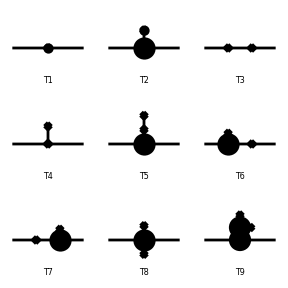

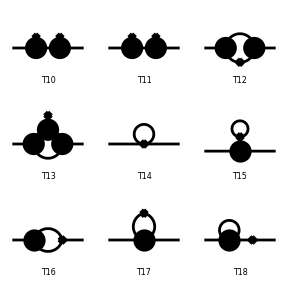

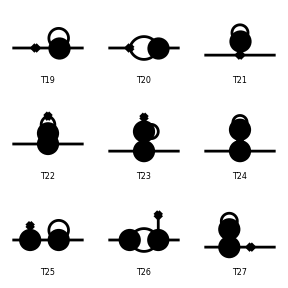

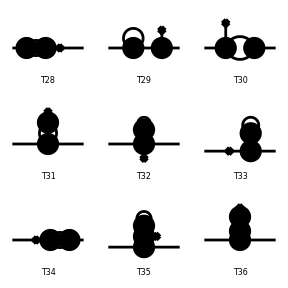

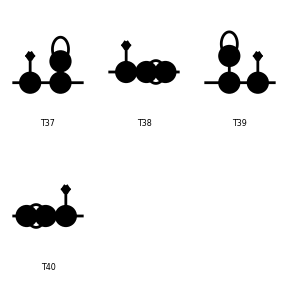

```mathematica
Topology1LoopFermionicSelfEnergyCorrection=CreateCTTopologies[2,1->1];
Paint[Topology1LoopFermionicSelfEnergyCorrection];
```

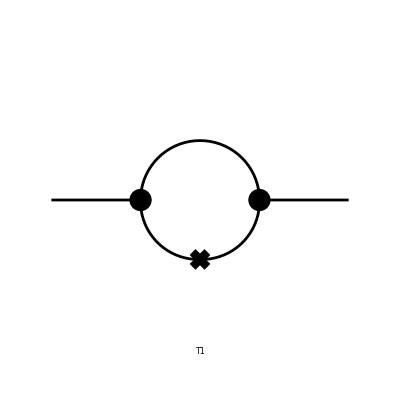

FeynArtsGraphics(1→1)(([T1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
CorrectionForRainbowDiagramTopology=Take[Topology1LoopFermionicSelfEnergyCorrection,{12}];
Paint[CorrectionForRainbowDiagramTopology]
```

```mathematica
(*Field insertion*)
```

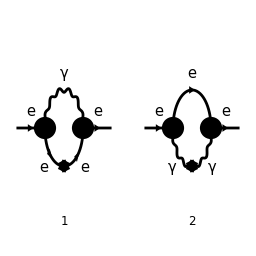

```mathematica
BubbleCounterTerms=InsertFields[CorrectionForRainbowDiagramTopology,Processee,ExcludeParticles->{S[_],V[2|3],(S|U)[_],F[3|4],F[2,{2|3}]}];
Paint[BubbleCounterTerms,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

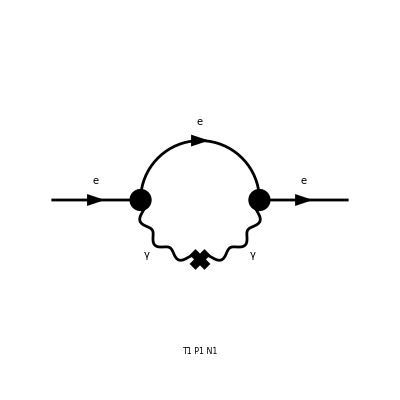

FeynArtsGraphics({e}→{e})(([T1 P1 N1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
FermionLoopDiagramCounterTerm=DiagramExtract[BubbleCounterTerms,{2}];
Paint[FermionLoopDiagramCounterTerm]
```

#### Amplitude

```mathematica
FAamplEBCT=CreateFeynAmp[FermionLoopDiagramCounterTerm,Truncated->True,GaugeRules->{},PreFactor->1];
convertamplEBCT=FCFAConvert[FAamplEBCT,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{l},LorentzIndexNames->{μ,ν,α,β},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,DropSumOver->True,Contract->True,FinalSubstitutions->{Zm->SMP["Z_m"],Zpsi->SMP["Z_psi"],ZA->SMP["Z_A"],Zxi->SMP["Z_xi"],GaugeXi[V[1]]->1}];
convertamplEBCTmassless=convertamplEBCT//.SMP["m_e"]->0
```

(e^2 (l̄)^2 Z_A (γ̄)^ν.(γ̄·(l̄+p̄)).(γ̄)^ν)/(((l̄)^2)^2.(l̄+p̄)^2)+(e^2 Z_A (γ̄·l̄).(γ̄·(l̄+p̄)).(γ̄·l̄))/(Z_ξ ((l̄)^2)^2.(l̄+p̄)^2)-(e^2 Z_A (γ̄·l̄).(γ̄·(l̄+p̄)).(γ̄·l̄))/(((l̄)^2)^2.(l̄+p̄)^2)+-(e^2 (l̄)^2 (γ̄)^ν.(γ̄·(l̄+p̄)).(γ̄)^ν)/(((l̄)^2)^2.(l̄+p̄)^2)

```mathematica
AlgebraDiracmasslessCTEB1=DiracSimplify[convertamplEBCTmassless];
AlgebraDiracmasslessCTEB2=DiracSimplify[AlgebraDiracmasslessCTEB1]
```

(2 e^2 Z_A γ̄·l̄ (l̄·p̄))/(Z_ξ ((l̄)^2)^2.(l̄+p̄)^2)+(e^2 (l̄)^2 Z_A γ̄·l̄)/(Z_ξ ((l̄)^2)^2.(l̄+p̄)^2)-(e^2 (l̄)^2 Z_A γ̄·p̄)/(Z_ξ ((l̄)^2)^2.(l̄+p̄)^2)-(2 e^2 Z_A γ̄·l̄ (l̄·p̄))/(((l̄)^2)^2.(l̄+p̄)^2)-(3 e^2 (l̄)^2 Z_A γ̄·l̄)/(((l̄)^2)^2.(l̄+p̄)^2)-(e^2 (l̄)^2 Z_A γ̄·p̄)/(((l̄)^2)^2.(l̄+p̄)^2)+(2 e^2 (l̄)^2 γ̄·l̄)/(((l̄)^2)^2.(l̄+p̄)^2)+(2 e^2 (l̄)^2 γ̄·p̄)/(((l̄)^2)^2.(l̄+p̄)^2)

```mathematica
{irrelevantmasslessIREGCTEB,loopsmasslessCTEB,THEUNIQUEIREGINTEGRALSmasslessCTEB}=FCLoopExtract[AlgebraDiracmasslessCTEB2,{l},loopHeadIREGmasslessCTEB];
IREGINTEGRALSEBmasslessCCTEB=THEUNIQUEIREGINTEGRALSmasslessCTEB/.loopHeadIREGmasslessCTEB->Identity
```

{(l̄)^2/(((l̄)^2)^2.(l̄+p̄)^2),((l̄)^2 γ̄·l̄)/(((l̄)^2)^2.(l̄+p̄)^2),(γ̄·l̄ (l̄·p̄))/(((l̄)^2)^2.(l̄+p̄)^2)}

#### Replacements

```mathematica
CTATerm=FeynAmpDenominator[PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l+p],0]] Pair[Momentum[l],Momentum[l]]
```

(l̄)^2/(((l̄)^2)^2.(l̄+p̄)^2)

```mathematica
CTCTerm=DiracGamma[Momentum[l]] FeynAmpDenominator[PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l+p],0]]Pair[Momentum[l],Momentum[p]]
```

(γ̄·l̄ (l̄·p̄))/(((l̄)^2)^2.(l̄+p̄)^2)

```mathematica
CTBTerm=DiracGamma[Momentum[l]] FeynAmpDenominator[PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l],0],PropagatorDenominator[Momentum[l+p],0]] Pair[Momentum[l],Momentum[l]]
```

((l̄)^2 γ̄·l̄)/(((l̄)^2)^2.(l̄+p̄)^2)

```mathematica
(*What I computed by hand*)
```

```mathematica
CTBReplace=-DiracGamma[Momentum[p]]/2*(Ilogλ2-b*Log[-p^2/λ^2]+2*b)
```

-1/2 γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)

```mathematica
CTATermReplace=Ilogλ2-b*Log[-p^2/λ^2]+2*b
```

b (-log(-p^2/λ^2))+2 b+Ilogλ2

```mathematica
CTCTermReplace=DiracGamma[Momentum[p]]*1/4*(Ilogλ2-b*Log[-p^2/λ^2]+2*b)+(DiracGamma[Momentum[p]]*b)/2
```

1/4 γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)+1/2 b γ̄·p̄

```mathematica
(*Substitution rule for the rainbow C.T*)
```

```mathematica
SubRuleforElectronBubbleCT={CTBTerm->CTBReplace,CTATerm->CTATermReplace,CTCTerm->CTCTermReplace};
```

```mathematica
(*The final electron bubble C.T*)
```

```mathematica
ElectronBubbleCounterTermFinal=AlgebraDiracmasslessCTEB2//.SubRuleforElectronBubbleCT
```

-(3 e^2 Z_A γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2))/(2 Z_ξ)+(2 e^2 Z_A (1/4 γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)+1/2 b γ̄·p̄))/Z_ξ+1/2 e^2 Z_A γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)-2 e^2 Z_A (1/4 γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)+1/2 b γ̄·p̄)+e^2 γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)

```mathematica
(*The renormalization constants and others IREG*)
```

```mathematica
GaugeZxi={SMP["Z_xi"]->SMP["Z_A"]};
```

```mathematica
ElectronBubbleCounterTermFinal2=ElectronBubbleCounterTermFinal//.GaugeZxi
```

1/2 e^2 Z_A γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)-2 e^2 Z_A (1/4 γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)+1/2 b γ̄·p̄)-1/2 e^2 γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)+2 e^2 (1/4 γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)+1/2 b γ̄·p̄)

```mathematica
Z3=1+SMP["e"]^2*SMP["d_A"]
```

e^2 δ_A+1

```mathematica
NewRuleCTElectronBubble={SMP["Z_A"]->Z3};
```

```mathematica
ElectronBubbleCounterTermFinal3=ElectronBubbleCounterTermFinal2//.NewRuleCTElectronBubble
```

1/2 e^2 (e^2 δ_A+1) γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)-2 e^2 (e^2 δ_A+1) (1/4 γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)+1/2 b γ̄·p̄)-1/2 e^2 γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)+2 e^2 (1/4 γ̄·p̄ (b (-log(-p^2/λ^2))+2 b+Ilogλ2)+1/2 b γ̄·p̄)

```mathematica
ElectronBubbleCounterTermFinal4=Simplify[ElectronBubbleCounterTermFinal3]
```

-b e^4 δ_A γ̄·p̄

## Renormalization

```mathematica
(*If everything is well, non-local terms should cancel*)
```

```mathematica
(*Before doing this, let's put some definitions for the counter-terms. All of them where taken for our Symmetry paper*)
```

```mathematica
CounterTermDeltaAQED=I*4/3*Ilogλ2
```

(4 ⅈ Ilogλ2)/3

```mathematica
(*Now, the substitution rules*)
```

```mathematica
RuleCTCoupling={SMP["d_A"]->CounterTermDeltaAQED};
```

```mathematica
(*Re-writting the counterterm*)
```

```mathematica
ElectronBubbleCounterTermFinal5=ElectronBubbleCounterTermFinal4//.RuleCTCoupling
```

-4/3 ⅈ b e^4 Ilogλ2 γ̄·p̄

```mathematica
(*Regulated Amplitude + Counter-Term*)
```

```mathematica
ChaveBubble=RegulatedElectronBubbleAmplitudeIREG+ElectronBubbleCounterTermFinal5
```

2/3 ⅈ b e^4 Ilogλ2 γ̄·p̄

```mathematica
ChaveBubble2=Simplify[ChaveBubble]
```

2/3 ⅈ b e^4 Ilogλ2 γ̄·p̄